#### Sequential rule

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Medium],GrayLevel[.9], Haloing[Red, 1.25]],"ArrowDirection"->Left,"InitialIndex"->0, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[2]]
]
```

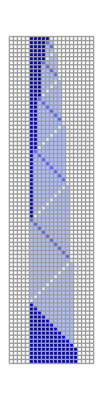

```mathematica
{{"[◼]", "PerturbedArrayPlot"}}[#1, If[#2 == <||>, {}, First[Keys[#2]]], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]]&@@[{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, {Join[Table[1,5],{2}],0},{80,{-5, 15}}, <||>]
```

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-5, 15}}, <||>]], 6];
outputs = Length[First[[rule, {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}, #]]&/@ aps;
```

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 6];outputs = If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[First[[rule, {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}, #]]]&/@ aps];
```

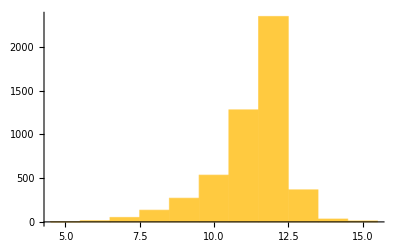

```mathematica
Histogram[outputs, {1}, PlotRange->All]
```

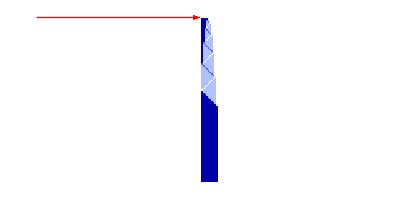
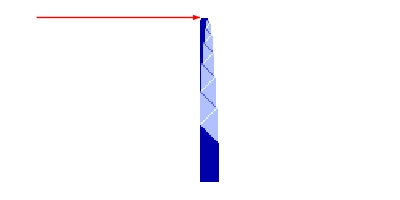
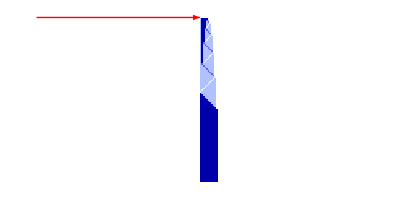
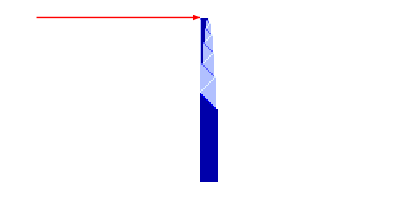
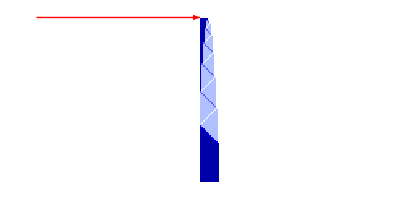
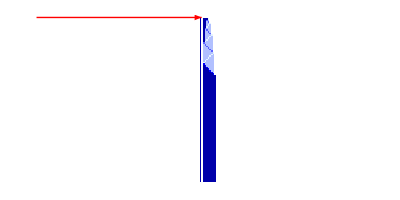
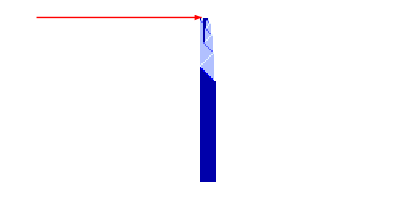
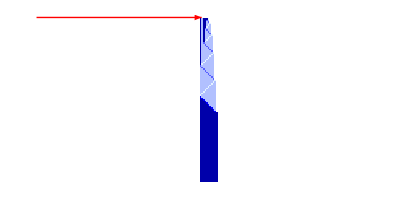

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 6];({{"[◼]", "PerturbedArrayPlot"}}[#1, If[#2 == <||>, {}, First[Keys[#2]]], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->False]&@@[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, #]&)/@ aps[[;;10]]]
```

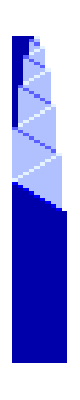
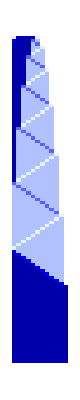
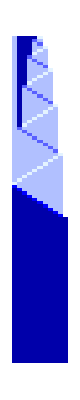
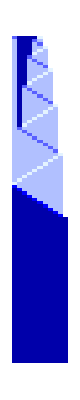
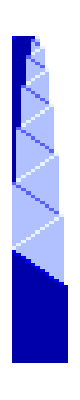
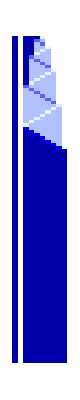
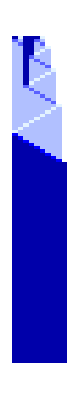
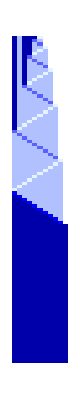

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 6];(ArrayPlot[ArrayPad[#, 1]&/@ResourceFunction["ArrayCrop"][#], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->False]&@@[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, #]&)/@ aps[[;;10]]]
```

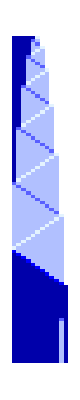
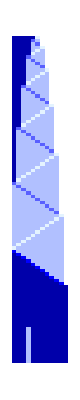
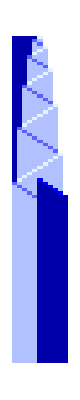
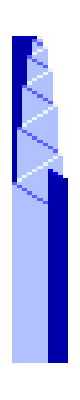
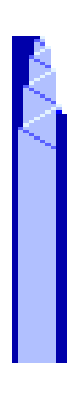
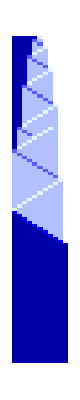
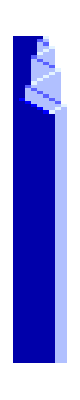
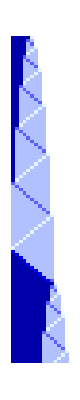

```mathematica
SeedRandom[44356];Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 6];(ArrayPlot[ArrayPad[#, 1]&/@ResourceFunction["ArrayCrop"][#], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->False]&@@[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, #]&)/@ RandomSample[aps, 100]]
```

```mathematica
SeedRandom[44356];FeatureSpacePlot[Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 6];(ArrayPlot[ArrayPad[#, 1]&/@ResourceFunction["ArrayCrop"][#], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->False]&@@[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, #]&)/@ RandomSample[aps, 100]]]
```

-Graphics-

```mathematica
SeedRandom[1111];
rand=RandomSample[{{"[◼]", "allperts"}}[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{102,{-200,200}}],4],400];Magnify[Module[{ru={299459058088077823758143088095350287424,4,1}},FeatureSpacePlot[With[{pca={{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{102,{-200,200}},#,"ReturnPerturbations"->False]},Rasterize[{{"[◼]", "PlotCA"}}[pca]]->{{"[◼]", "PlotCA"}}[pca,"Trim"->{3,None}]]&/@rand,LabelingSize->100,PlotStyle->AbsolutePointSize[9],Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453,PerformanceGoal->"Static",ImageSize->2000]],.31]
```

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 6];({{"[◼]", "PerturbedArrayPlot"}}[#1, If[#2 == <||>, {}, First[Keys[#2]]], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->False]&@@[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, #]&)/@ RandomSample[aps, 30]]
```

#### Parallel rule

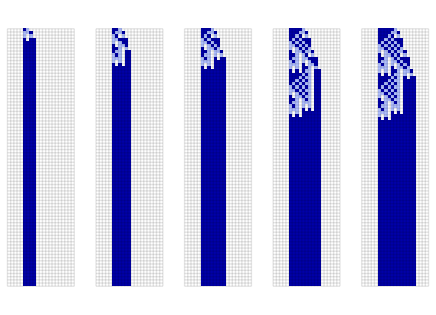

```mathematica
SeedRandom[111000+8];Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{30,9}->2|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[1]]
]
```